```mathematica
Clear["`*"]
```

```mathematica
<<PlotLegends`
```

# Spencer Lyon

## Physics 330

Lab 4

## P4.1

### a.)

```mathematica
ω0 = 2;
```

```mathematica
ops = {StreamPoints->Fine, VectorScale->Small, VectorStyle->Orange};
```

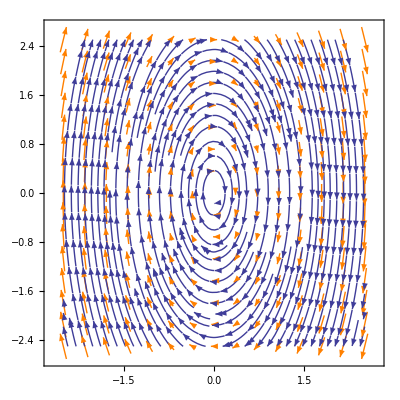

```mathematica
flow = VectorPlot[{v, - ω0^2 x},{x,-2.5,2.5},{v,-2.5,2.5}, Evaluate[ops]]
```

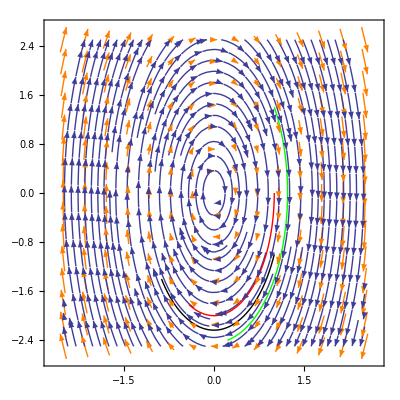

```mathematica
eqns = {D[x[t],{t,1}]==v[t], D[v[t],{t,1}]== - ω0^2*x[t], x[0]==1, v[0]==v0};
case1 = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->0, {x[t], v[t]},{t,0,1}]];
case2 = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->1.4, {x[t], v[t]},{t,0,1}]];
case3 = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->-1, {x[t], v[t]},{t,0,1}]];

t1 = ParametricPlot[case1,{t,0,1}, PlotStyle->{Red, Thick}];
t2 = ParametricPlot[case2,{t,0,1}, PlotStyle->{Green, Thick}];
t3 = ParametricPlot[case3,{t,0,1},PlotStyle->{Black,Thick}];
Show[{flow,t2,t1,t3}]
```

### b.)

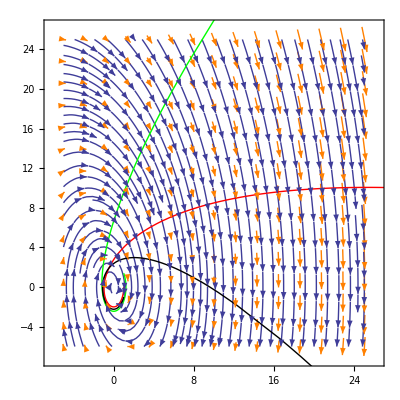

```mathematica
γ = 0.5; plotRange = 25;
flowb = VectorPlot[{v, - ω0^2 x - 2* γ * v},{x,-5,plotRange},{v,-6,plotRange}, Evaluate[ops]];
eqnsb = {D[x[t],{t,1}]==v[t], D[v[t],{t,1}]== - ω0^2*x[t] - 2 *γ *v[t], x[0]==1, v[0]==v0};
case1b = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->0, {x[t], v[t]},{t,0,20}]];
case2b = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->1.4, {x[t], v[t]},{t,0,20}]];
case3b = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->-1, {x[t], v[t]},{t,0,20}]];

t1b = ParametricPlot[case1,{t,0,20}, PlotStyle->{Red, Thick}];
t2b = ParametricPlot[case2,{t,0,20}, PlotStyle->{Green, Thick}];
t3b = ParametricPlot[case3,{t,0,20},PlotStyle->{Black,Thick}];
Show[{flowb,t2b,t1b,t3b}]
```

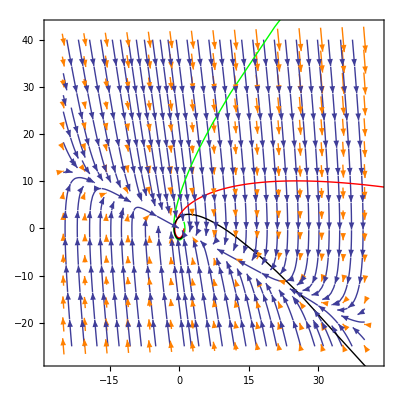

```mathematica
γ2 = 4.0; plotRange = 40;
flowb2 = VectorPlot[{v, - ω0^2 x - 2* γ2 * v},{x,-25,plotRange},{v,-25,plotRange}, Evaluate[ops]];
eqnsb2 = {D[x[t],{t,1}]==v[t], D[v[t],{t,1}]== - ω0^2*x[t] - 2 *γ2 *v[t], x[0]==1, v[0]==v0};
case1b2 = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->0, {x[t], v[t]},{t,0,20}]];
case2b2 = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->1.4, {x[t], v[t]},{t,0,20}]];
case3b2 = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->-1, {x[t], v[t]},{t,0,20}]];

t1b2 = ParametricPlot[case1,{t,0,20}, PlotStyle->{Red, Thick}];
t2b2 = ParametricPlot[case2,{t,0,20}, PlotStyle->{Green, Thick}];
t3b2 = ParametricPlot[case3,{t,0,20},PlotStyle->{Black,Thick}];
Show[{flowb2,t2b2,t1b2,t3b2}]
```

### c.)

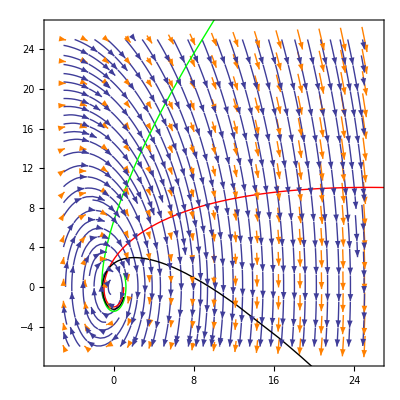

```mathematica
γc = 0.5; plotRange = 25;
flowc = VectorPlot[{v, - ω0^2 x - 2* γc *Abs[ v]/1},{x,-5,plotRange},{v,-6,plotRange}, Evaluate[ops]];
eqnsc = {D[x[t],{t,1}]==v[t], D[v[t],{t,1}]== - ω0^2*x[t] - 2 *γc *Abs[v[t]]/1, x[0]==1, v[0]==v0};
case1c= {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->0, {x[t], v[t]},{t,0,20}]];
case2c = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->1.4, {x[t], v[t]},{t,0,20}]];
case3c = {x[t],v[t]}/.Flatten[NDSolve[eqns/.v0->-1, {x[t], v[t]},{t,0,20}]];

t1c = ParametricPlot[case1,{t,0,20}, PlotStyle->{Red, Thick}];
t2c = ParametricPlot[case2,{t,0,20}, PlotStyle->{Green, Thick}];
t3c = ParametricPlot[case3,{t,0,20},PlotStyle->{Black,Thick}];
Show[{flowc,t2c,t1c,t3c}]
```